Subintervall: {1,400}

Genutzte Eigenwerte (N): 400

Erster Eigenwert im Fit: 5.30472

Letzter Eigenwert im Fit: 161.128

--- 3-Term-Weyl-Fit mit Regularisierung ---

Fenster (k/N): {0.2,0.9}

A0 (LS, reg): 0.2359754685

A1 (LS, reg): -0.5179079277

A2 (LS, reg): -0.0704180782

Volumen (aus Spektrum, 3-Term): 13.9739

Volumen (geometrisch):          14.4513

Relativer Fehler:               0.0330364

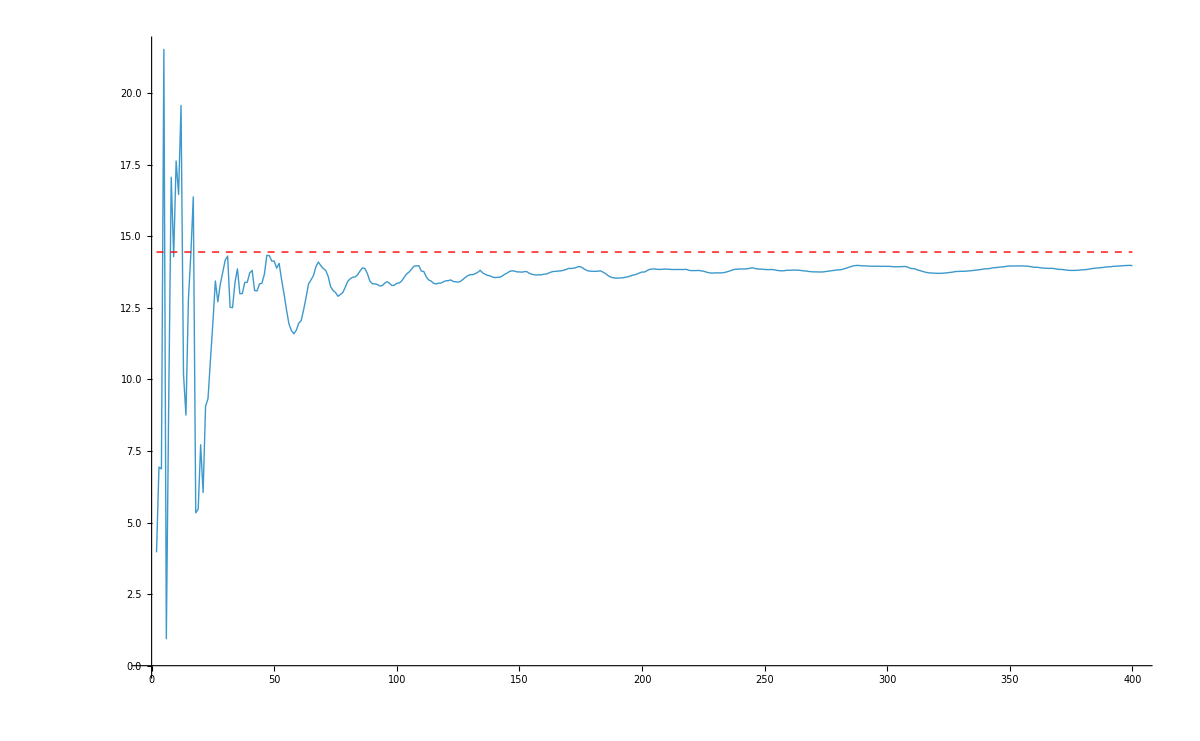

```mathematica
Clear["Global`*"];
Needs["NDSolve`FEM`"];

eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\mathematica\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1800.txt";

eigsIndexRange={1,400};
(* Eigenwerte einlesen *)
targetEigenvaluesRaw=Import[eigenvalueFilePath,"Table"]//Flatten;
targetEigenvalues=targetEigenvaluesRaw[[eigsIndexRange[[1]];;eigsIndexRange[[2]]]];
numEigs=Length[targetEigenvalues];

Print["Subintervall: ",eigsIndexRange];
Print["Genutzte Eigenwerte (N): ",numEigs];
Print["Erster Eigenwert im Fit: ",First[targetEigenvalues]];
Print["Letzter Eigenwert im Fit: ",Last[targetEigenvalues]];

(* Hauptfenster für finale Ergebnisse *)
fitFracRangeMain={0.2,0.9};
lambdaReg=10^-6;

(* eigs:Liste der Eigenwerte λ_k (sortiert) fracRange:[r1,r2] mit
0<r1<r2≤1 für k-Bereich k/N lambdaReg:Regularisierungsstärke (Tikhonov) auf Einheitsmatrix *)
fitWeyl3LSreg[eigs_List,fracRange_:{0.2,0.9},lambdaReg_:10^-6]:=Module[{n,kMin,kMax,lamVals,kVals,X,ATA,ATy,reg,coeffs},n=Length[eigs];
kMin=Ceiling[fracRange[[1]] n];
kMax=Floor[fracRange[[2]] n];
(* Spektral-Fenster auswählen *)
lamVals=N@eigs[[kMin;;kMax]];
kVals=N@Range[kMin,kMax];
(* Design-Matrix:Zeilen={λ^(3/2),λ,√λ} *)
X=Transpose@{lamVals^(3/2),lamVals,Sqrt[lamVals]};
(* Normalengleichungen *)
ATA=Transpose[X].X;(* 3x3 *)
ATy=Transpose[X].kVals;(* 3x1 *)
(* Mini-Regularisierung:λ*I,skaliert mit mittlerer Diagonale *)
reg=lambdaReg*Mean[Diagonal[ATA]]*IdentityMatrix[Length[Diagonal[ATA]]];
coeffs=LinearSolve[ATA+reg,ATy];
coeffs];

(* Volumen aus spektralem A0-Term *)
(* Fit auf festem "ehrlichen" Fenster {0.2,0.9} *)
{A0fit,A1fit,A2fit}=fitWeyl3LSreg[targetEigenvalues,fitFracRangeMain,lambdaReg];
volSpec=6 Pi^2 A0fit;

(* Wahre Achsen *)
trueA=1.0;
trueB=1.5;
trueC=2.3;
volTrue=4 Pi/3 trueA trueB trueC;

Print[""];
Print["--- 3-Term-Weyl-Fit mit Regularisierung ---"];
Print["Fenster (k/N): ",fitFracRangeMain];
Print["A0 (LS, reg): ",NumberForm[A0fit,10]];
Print["A1 (LS, reg): ",NumberForm[A1fit,10]];
Print["A2 (LS, reg): ",NumberForm[A2fit,10]];
Print["Volumen (aus Spektrum, 3-Term): ",NumberForm[volSpec,6]];
Print["Volumen (geometrisch):          ",NumberForm[volTrue,6]];
Print["Relativer Fehler:               ",NumberForm[Abs[volSpec-volTrue]/volTrue,6]];

(* Konvergenz der Volumenschätzung:nur die ersten m Eigenwerte verwenden und m wachsen lassen *)
maxN=Length[targetEigenvalues];
(* ab m=2,weil das Fenster {0.2,0.9} sonst kein sinnvolles k-Intervall hat *)
volConvData=Table[
Module[{eigsSub,coeffs,A0,vol},
eigsSub=targetEigenvalues[[1;;m]];
coeffs=fitWeyl3LSreg[eigsSub,fitFracRangeMain,lambdaReg];
A0=coeffs[[1]];
vol=6 Pi^2 A0;
{m,vol}],
{m,2,maxN}];

convPlot=Show[
{
ListLinePlot[
volConvData,
PlotRange->All,
(* AxesLabel->{Style["N (Anzahl erster Eigenwerte)",14],Style["Volumen aus Weyl-Fit V_N",14]}, *)
(* PlotLabel->Style["Konvergenz der Volumenschätzung aus 3-Term-Weyl-Fit",16], *)
ImageSize->1200,
PlotStyle->Thick],
Plot[volTrue,{x,2,maxN},PlotStyle->{Red,Dashed,Thick}]
},
PlotLegends->Placed[
{Style["V_N aus Spektrum",12],Style["Wahres Volumen V_true",12]},
{0.8,0.2}  (* rechts unten in der Grafik *)],
ImageSize->1200];
convPlot
```